# Finding Hidden Structure in a NN (MNIST)

First, load the data and define the NetEncoder/NetDecoder

```mathematica
trainingData=ResourceData["MNIST","TrainingData"];
testData=ResourceData["MNIST","TestData"];
mnistEncoder=NetEncoder[{"Image",{28,28},"ColorSpace"->"Grayscale"}];
mnistDecoder=NetDecoder[{"Class",Range[0,9]}];
```

We’ll slightly modify the Neural Network from yesterday to see more examples.

```mathematica
uNet=NetChain[{
ConvolutionLayer[21,{9,9}],
ConvolutionLayer[15,{7,7}],
FunctionLayer[Ramp],
LinearLayer[10],
SoftmaxLayer[]
},
"Input"->mnistEncoder,
"Output"->mnistDecoder];
```

The process of building a Network graph and training the Neural Network is similar.

```mathematica
iNet=NetInitialize[uNet];
tNet=NetGraph[<|"MyNet"->iNet,"loss"->CrossEntropyLossLayer["Index"]|>,{NetPort["Input"]->"MyNet"->NetPort["loss","Input"],NetPort["Target"]->NetPort["loss","Target"]}];

trainAssoc=<|"Input"->Keys[trainingData],"Target"->Values[trainingData]+1|>;
testAssoc=<|"Input"->Keys[testData],"Target"->Values[testData]+1|>;


results=NetTrain[tNet,trainAssoc,All,ValidationSet->testAssoc,MaxTrainingRounds->5]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:4690  rounds:5  time:2.5min  examples/s:2028
data | ,,  training examples:60000  validation examples:10000  processed examples:300160  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:4.73×10^-2  error:1.43%
validation | ,,  loss:8.08×10^-2  error:2.21%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
NetTrainResultsObject[{{"NetTrain Results"}, {{{summary, ,"," " "batches:3792 " "rounds:4 " "time:11min " "examples/s:360}, {data, ,"," " "training examples:60000 " "validation examples:10000 " "processed examples:242688 " "skipped examples:0}, {method, ,"," " "ADAMoptimizer " "batch size64CPU}, {round, ,"," " "loss:"5.53"×10^("-2") " "error:1.58%}, {validation, ,"," " "loss:"1.62"×10^("-1") " "error:3.24%}, {, }, {-Graphics-  "training set"	-Graphics-  "validation set", }}}}]
```

```mathematica
tdNet=NetExtract[results["TrainedNet"],"MyNet"];
tdNet=NetReplacePart[tdNet,{"Input"->mnistEncoder,"Output"->mnistDecoder}];
```

## Measurements

ClassifierMeasurements performs a variety of statistical measurements on our trained Neural Network.

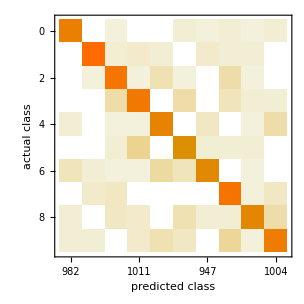
Classifier Measurements
Classifier method | Net
Number of test examples | 10000
Accuracy | (98.130.14) %
Accuracy baseline | (11.350.32) %
Geometric mean of probabilities | 0.937 ± 0.0046
Mean cross entropy | 0.0651 ± 0.0049
Single evaluation time | 3.13 ms/example
Batch evaluation speed | 7.35 examples/ms
-Graphics- |

```mathematica
measurements=ClassifierMeasurements[tdNet,testData]
```

```mathematica
measurements["Accuracy"]
measurements["WorstClassifiedExamples"]
```

0.9813

{-Graphics-→6,-Graphics-→2,-Graphics-→6,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→6,-Graphics-→8,-Graphics-→6,-Graphics-→3}

```mathematica
measurements["LeastCertainExamples"]
```

{-Graphics-→6,-Graphics-→1,-Graphics-→5,-Graphics-→9,-Graphics-→4,-Graphics-→6,-Graphics-→6,-Graphics-→7,-Graphics-→6,-Graphics-→7}

```mathematica
measurements["TopConfusions"]
```

{2→7,3→5,4→9,8→9,2→4,3→7,4→6,7→9,1→3,1→6}

## Finding Hidden Features

NetMeasurements can also plot the mean activation of the results after a certain number of layers. Here are the mean activations after the first convolutional layer with 6 channels.

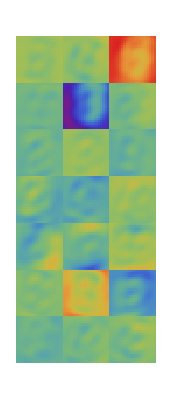

```mathematica
activations1=NetMeasurements[tdNet,testData,NetPort[{1,"Output"}]];
ArrayPlot[ArrayFlatten@Partition[activations1,3],ColorFunction->"Rainbow",FrameTicks->None]
```

Activations after the fourth layer. At this level the output is a convolution with three channels.

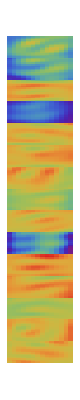

```mathematica
activations4=NetMeasurements[tdNet,testData,NetPort[{2,"Output"}]];
ArrayPlot[Flatten[activations4,1],ColorFunction->"Rainbow",FrameTicks->None]
```

```mathematica
activations3=NetMeasurements[tdNet,testData,NetPort[{5,"Output"}]];
ArrayPlot[Partition[activations1,3]]
```

-Graphics-

```mathematica
tNet
```

NetGraph[…]